```mathematica
Integrate[
PDF[NormalDistribution[],x], x]
```

1/2 Erf[x/(√2)]

```mathematica
FullSimplify[
Normalize[D[{x,1/2 Erf[x/(√2)]},x]], x∈Reals]
```

{1/(√(1+(ⅇ^(-x^2))/(2 π))),(ⅇ^(-x^2/2))/(√(ⅇ^(-x^2)+2 π))}

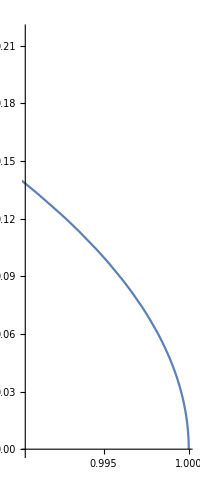

```mathematica
ParametricPlot[
{1/(√(1+(ⅇ^(-x^2))/(2 π))),(ⅇ^(-x^2/2))/(√(ⅇ^(-x^2)+2 π))},
{x, 0, 10}]
```



```mathematica
Plot[x^2,{x, -2, 2}]
```

```mathematica
{a,a^2}-{x,x^2}
```

{a-x,a^2-x^2}

```mathematica
{a,f[a]}-{0,f[0]}
```

{a,-f[0]+f[a]}

```mathematica
{a-x,a^2-x^2}
```

{a-x,a^2-x^2}

```mathematica
{a-b,f[a]-f[b]}
```

{a-b,f[a]-f[b]}

```mathematica
With[{f=#^2&, a=1, b=0},
{a-b,f[a]-f[b]}]
```

{1,1}

```mathematica
Manipulate[
Show[{
Plot[x^2, {x, -2, 2}],
ListPlot[{{a, a^2}, {b, b^2}}]}],
{a, 0, 2}, {b, 1, 2}]
```

```mathematica
Manipulate[
Show[{
Plot[{x^2,(b^2-a^2)/(b-a)x}, {x, -2, 2}],
ListPlot[{{a, a^2}, {b, b^2}}]}],
{a, 0, 2}, {b, 0, 2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[
Show[{
Plot[{x^2,(b^2-a^2)/(b-a)x}, {x, -2, 2}],
ListPlot[{{a, a^2}, {b, b^2}}]}, PlotRange->{0, 4}],
{a, 0, 2}, {b, 0, 2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[{
Integrate[b^2/b x, {x, 0, b}],
Show[{
Plot[{x^2,b^2/b x}, {x, -2, 2}],
ListPlot[{{0,0}, {b, b^2}}]}, PlotRange->{0, 4}]},
{b, 0, 2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[{
Integrate[b^2/b x, {x, 0, b}],
Show[{
Plot[{x^2,b^2/b x}, {x, -2, 2}],
ListPlot[{{0,0}, {b, b^2}}]}, PlotRange->{0, 4}]},
{b, 0.01, 2}]
```

```mathematica
Laplacian[f[x,y], {x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

```mathematica
Plot3D[Sin[x]x, {x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x]x], {x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x]x y], {x,y}∈Disk[{0,0}, 3]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x]x y], {x,y}∈Disk[{0,0}, 10]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x y]], {x,y}∈Disk[{0,0}, 10]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x y]]/Cos[x y], {x,y}∈Disk[{0,0}, 10]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[Sin[x y]]/Cos[x y], {x,y}∈Disk[{0,0}, 2]]
```

-Graphics3D-

```mathematica
Laplacian[Exp[Sin[x y]]/Cos[x y], {x,y}]
```

ⅇ^Sin[x y] x^2 Cos[x y]+ⅇ^Sin[x y] y^2 Cos[x y]+ⅇ^Sin[x y] x^2 Sec[x y]^3+ⅇ^Sin[x y] y^2 Sec[x y]^3+ⅇ^Sin[x y] x^2 Tan[x y]+ⅇ^Sin[x y] y^2 Tan[x y]+ⅇ^Sin[x y] x^2 Sec[x y] Tan[x y]^2+ⅇ^Sin[x y] y^2 Sec[x y] Tan[x y]^2

```mathematica
Plot3D[ⅇ^Sin[x y] x^2 Cos[x y]+ⅇ^Sin[x y] y^2 Cos[x y]+ⅇ^Sin[x y] x^2 Sec[x y]^3+ⅇ^Sin[x y] y^2 Sec[x y]^3+ⅇ^Sin[x y] x^2 Tan[x y]+ⅇ^Sin[x y] y^2 Tan[x y]+ⅇ^Sin[x y] x^2 Sec[x y] Tan[x y]^2+ⅇ^Sin[x y] y^2 Sec[x y] Tan[x y]^2,{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
alphas=Range[0,20,.001];
betas=ConstantArray[0.01,Length[alphas]];
anglepath=AnglePath3D[Transpose[{alphas,betas,betas}]];
line=Line[anglepath,VertexColors->Table[ColorData["DarkRainbow"][i/Length[anglepath]],{i,Length[anglepath]}]];
```

```mathematica
%28
```

{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,19981,19.991,19.992,19.993,19.994,19.995,19.996,19.997,19.998,19.999,20.}
 |  |  |  |

```mathematica
ArcLength[line]
```

20001.

```mathematica
Graphics3D[{Thickness[.005],line},Boxed->False]
```

-Graphics3D-

```mathematica
Show[%34,Boxed->True]
```

-Graphics3D-

```mathematica
net=NetModel["Unguided Volumetric Regression Net for 3D Face Reconstruction"]
```

NetChain[<>]

```mathematica
img = -Graphics-
```

-Graphics-

```mathematica
img3D=Image3D[255 Transpose@Normal[net[img]],"Byte"];
reconstruction=ImageResize[img3D,Insert[ImageDimensions[img],100,2]]
```

-Graphics3D-

```mathematica
mesh=ImageMesh[reconstruction,Method->"DualMarchingCubes"]
```

-Graphics3D-

```mathematica
poly=CanonicalizePolyhedron[mesh]
```

Polyhedron[…]

```mathematica
Graphics3D[{Texture[img],EdgeForm[],Append[poly,VertexTextureCoordinates->Transpose[Apply[Rescale[#,{0,#2},{0,1}]&,Transpose[{Part[Transpose[PolyhedronCoordinates[poly]],{1,3}],ImageDimensions[img]}],{1}]]]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Printout3D[mesh,"Sculpteo"]
```

Dataset[<>]